# EllipticIntegrals Paclet Examples

This notebook demonstrates how to load and use the ArnoudBuzing/EllipticIntegrals paclet.

## Loading the Paclet

Because the paclet functions match the built-in Wolfram Language function names (to avoid symbol shadowing conflicts), we load the package using an alias context ei`:

```mathematica
(* Load local paclet with alias *)
PacletDirectoryLoad[DirectoryName[NotebookDirectory[]]];
```

```mathematica
Needs["ArnoudBuzing`EllipticIntegrals`"->"ei`"]
```

## Legendre Complete Elliptic Integrals

The complete elliptic integrals are defined in terms of the parameter .

### Complete Elliptic Integral of the First Kind:

Evaluate $K(0.5)$ using the Rust binding:

```mathematica
ei`EllipticK[0.5]
```

1.85407

Compare with the built-in EllipticKpaclet:ref/EllipticKhttps://reference.wolfram.com/language/ref/EllipticK.html:

```mathematica
ei`EllipticK[0.5]-EllipticK[0.5]
```

4.44089×10^-16

### Complete Elliptic Integral of the Second Kind:

Evaluate $E(0.5)$:

```mathematica
ei`EllipticE[0.5]
```

1.35064

## Legendre Incomplete Elliptic Integrals

### Incomplete Elliptic Integral of the Second Kind:

Evaluate $E(1.0, 0.5)$:

```mathematica
ei`EllipticE[1.0,0.5]
```

0.92733

### Incomplete Elliptic Integral of the Third Kind:

Note that the argument order is consistent with the built-in EllipticPipaclet:ref/EllipticPihttps://reference.wolfram.com/language/ref/EllipticPi.html ():

```mathematica
ei`EllipticPi[0.2,1.0,0.5]
```

1.15207

## Bulirsch Elliptic Integrals

Bulirsch integrals provide high-speed, general representations of complete and incomplete elliptic integrals.

### Complete Integral Cel

Calculate Bulirsch's general complete elliptic integral :

```mathematica
ei`Cel[0.5,0.2,1.0,2.0]
```

9.70649

### Incomplete Integral El1

Evaluate Bulirsch's general incomplete elliptic integral of the first kind :

```mathematica
ei`El1[1.0,0.5]
```

0.851224

## Carlson Symmetric Integrals

Carlson symmetric integrals are highly robust and serve as the foundation of modern elliptic evaluation.

### Carlson $R_F(x, y, z)$

```mathematica
ei`CarlsonRF[1.0,2.0,3.0]
```

0.726946

### Error Handling

If invalid inputs are provided, the functions cleanly return Indeterminatepaclet:ref/Indeterminatehttps://reference.wolfram.com/language/ref/Indeterminate.html:

```mathematica
ei`CarlsonRF[1.0,2.0,-3.0]
```

Indeterminate

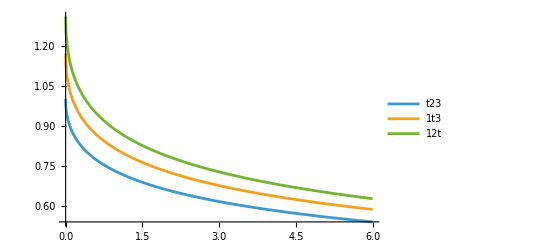

```mathematica
Plot[{CarlsonRF[t,2,3],CarlsonRF[1,t,3],CarlsonRF[1,2,t]},{t,0,6},PlotLegends->"Expressions"]
```

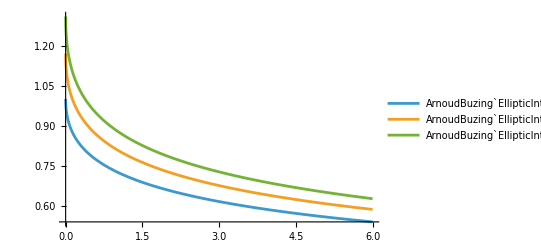

```mathematica
Plot[{ei`CarlsonRF[t,2,3],ei`CarlsonRF[1,t,3],ei`CarlsonRF[1,2,t]},{t,0,6},PlotLegends->"Expressions"]
```

```mathematica
ei`CarlsonRF
```

ArnoudBuzing`EllipticIntegrals`CarlsonRF